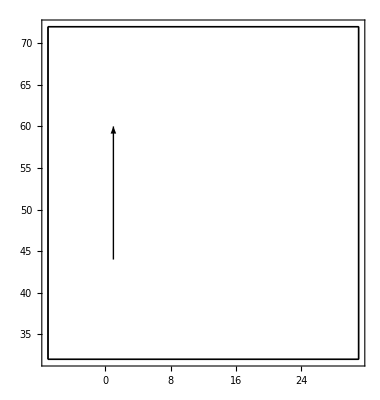

```mathematica
Graphics[Arrow[{{7,44},{7,60},{1,60}}],Frame->True];
Graphics[Arrow[{{1,44},{1,60}}],Frame->True];
LP = Graphics[Line[{{{-7,32},{31,32}},{{-7,32},{-7,72}},{{-7,72},{31,72}},{{31,72},{31,32}}}],Frame->True];
Show[%,%%,LP]
```

```mathematica
Evolucion1 = Import["/home/apu/Desktop/Prueba/Prueba1.dat","CSV"];
```

```mathematica
iteracion = 20 (*Numero de iteraciones que hago con el codigo python*);
```

```mathematica
Table[
Show[Graphics[
Arrow[{
{Evolucion1[[i]][[1]],Evolucion1[[i]][[2]]},
{Evolucion1[[i]][[3]],Evolucion1[[i]][[4]]}}],
Frame->True],LP]
,{i,1,iteracion}];
```

```mathematica
ListAnimate[%]
```

```mathematica
Quit
```